# True B-Spline Interpolation

## ▼ Continuous Uniform B-Spline basis function

## Spatial domain

```mathematica
bspline[n_,x_]=BSplineBasis[n-1,(x+n/2)/n];　(* 原点中心の一般的な B-Spline 関数 *)
```

```mathematica
𝒻CBS1[x_]=bspline[1,x];
𝒻CBS2[x_]=bspline[2,x];
𝒻CBS3[x_]=bspline[3,x];
𝒻CBS4[x_]=bspline[4,x];
𝒻CBS5[x_]=bspline[5,x];
𝒻CBS6[x_]=bspline[6,x];
```

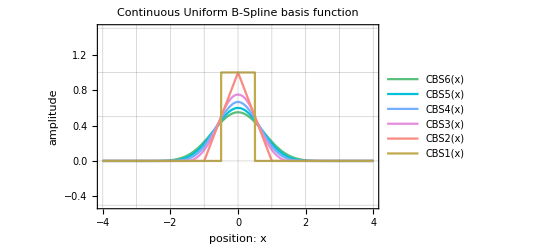

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline basis function (SD).svg

```mathematica
gra𝒻CBS1=Plot[Legended[𝒻CBS1[x],"CBS1(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
gra𝒻CBS2=Plot[Legended[𝒻CBS2[x],"CBS2(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
gra𝒻CBS3=Plot[Legended[𝒻CBS3[x],"CBS3(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
gra𝒻CBS4=Plot[Legended[𝒻CBS4[x],"CBS4(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
gra𝒻CBS5=Plot[Legended[𝒻CBS5[x],"CBS5(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
gra𝒻CBS6=Plot[Legended[𝒻CBS6[x],"CBS6(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
gra𝒻CBSs=Show[gra𝒻CBS6,gra𝒻CBS5,gra𝒻CBS4,gra𝒻CBS3,gra𝒻CBS2,gra𝒻CBS1,PlotLabel->"Continuous Uniform B-Spline basis function",Frame->True,FrameLabel->{"position: x","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline basis function (SD).svg"}],gra𝒻CBSs]
```

## Frequency domain

```mathematica
ℱCBS1[ω_]=FullSimplify[FourierTransform[𝒻CBS1[x],x,ω,FourierParameters->{1,-1}]]
ℱCBS2[ω_]=FullSimplify[FourierTransform[𝒻CBS2[x],x,ω,FourierParameters->{1,-1}]]
ℱCBS3[ω_]=FullSimplify[FourierTransform[𝒻CBS3[x],x,ω,FourierParameters->{1,-1}]]
ℱCBS4[ω_]=FullSimplify[FourierTransform[𝒻CBS4[x],x,ω,FourierParameters->{1,-1}]]
ℱCBS5[ω_]=FullSimplify[FourierTransform[𝒻CBS5[x],x,ω,FourierParameters->{1,-1}]]
ℱCBS6[ω_]=FullSimplify[FourierTransform[𝒻CBS6[x],x,ω,FourierParameters->{1,-1}]]
```

(2 Sin[ω/2])/ω

(2-2 Cos[ω])/ω^2

(8 Sin[ω/2]^3)/ω^3

(16 Sin[ω/2]^4)/ω^4

(32 Sin[ω/2]^5)/ω^5

(64 Sin[ω/2]^6)/ω^6

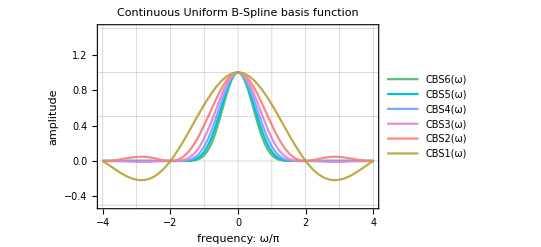

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline basis function (FD).svg

```mathematica
graℱCBS1=Plot[Legended[ℱCBS1[π ω],"CBS1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
graℱCBS2=Plot[Legended[ℱCBS2[π ω],"CBS2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
graℱCBS3=Plot[Legended[ℱCBS3[π ω],"CBS3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
graℱCBS4=Plot[Legended[ℱCBS4[π ω],"CBS4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graℱCBS5=Plot[Legended[ℱCBS5[π ω],"CBS5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
graℱCBS6=Plot[Legended[ℱCBS6[π ω],"CBS6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱCBS=Show[graℱCBS6,graℱCBS5,graℱCBS4,graℱCBS3,graℱCBS2,graℱCBS1,PlotLabel->"Continuous Uniform B-Spline basis function",Frame->True,FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline basis function (FD).svg"}],graℱCBS]
```

Uniform B-Spline curve

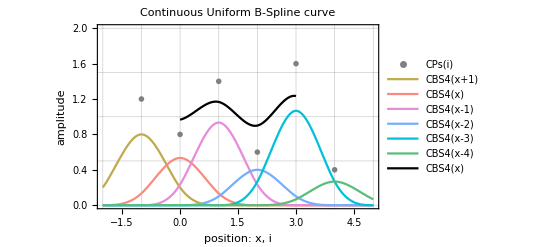

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline curve.svg

```mathematica
CPs={{-1,1.2},{0,0.8},{1,1.4},{2,0.6},{3,1.6},{4,0.4}};
𝒻BSB1[x_]:=CPs[[1,2]]*bspline[4,x+1];
𝒻BSB2[x_]:=CPs[[2,2]]*bspline[4,x-0];
𝒻BSB3[x_]:=CPs[[3,2]]*bspline[4,x-1];
𝒻BSB4[x_]:=CPs[[4,2]]*bspline[4,x-2];
𝒻BSB5[x_]:=CPs[[5,2]]*bspline[4,x-3];
𝒻BSB6[x_]:=CPs[[6,2]]*bspline[4,x-4];
𝒻BSBs[x_]:=𝒻BSB1[x]+𝒻BSB2[x]+𝒻BSB3[x]+𝒻BSB4[x]+𝒻BSB5[x]+𝒻BSB6[x];

graCPs:=ListPlot[Legended[CPs,"CPs(i)"],PlotRange->{{-2,+5},{0,2}},PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[128/255,128/255,128/255]}]
gra𝒻BSB1=Plot[Legended[𝒻BSB1[x],"CBS4(x+1)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
gra𝒻BSB2=Plot[Legended[𝒻BSB2[x],"CBS4(x)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
gra𝒻BSB3=Plot[Legended[𝒻BSB3[x],"CBS4(x-1)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
gra𝒻BSB4=Plot[Legended[𝒻BSB4[x],"CBS4(x-2)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
gra𝒻BSB5=Plot[Legended[𝒻BSB5[x],"CBS4(x-3)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
gra𝒻BSB6=Plot[Legended[𝒻BSB6[x],"CBS4(x-4)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
gra𝒻BSBs=Plot[Legended[𝒻BSBs[x],"CBS4(x)"],{x,0,3},PlotRange->{{-2,+5},{0,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,000/255,000/255]}];
gra𝒻BSC=Show[graCPs,gra𝒻BSB1,gra𝒻BSB2,gra𝒻BSB3,gra𝒻BSB4,gra𝒻BSB5,gra𝒻BSB6,gra𝒻BSBs,PlotLabel->"Continuous Uniform B-Spline curve",Frame->True,FrameLabel->{"position: x, i","amplitude"},GridLines->{Range[-2,+6,1],Range[0,+2,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline curve.svg"}],gra𝒻BSC]
```

## ▼ Discrete Uniform B-Spline basis function

## Spatial domain

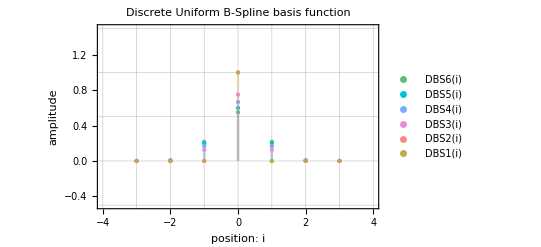

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete Uniform B-Spline basis function (SD).svg

```mathematica
gra𝒻DBS1=DiscretePlot[Legended[𝒻CBS1[x],"DBS1(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[192/255,170/255,076/255]}];
gra𝒻DBS2=DiscretePlot[Legended[𝒻CBS2[x],"DBS2(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[250/255,138/255,128/255]}];
gra𝒻DBS3=DiscretePlot[Legended[𝒻CBS3[x],"DBS3(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
gra𝒻DBS4=DiscretePlot[Legended[𝒻CBS4[x],"DBS4(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
gra𝒻DBS5=DiscretePlot[Legended[𝒻CBS5[x],"DBS5(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[000/255,193/255,215/255]}];
gra𝒻DBS6=DiscretePlot[Legended[𝒻CBS6[x],"DBS6(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[088/255,191/255,123/255]}];
gra𝒻DBS=Show[gra𝒻DBS6,gra𝒻DBS5,gra𝒻DBS4,gra𝒻DBS3,gra𝒻DBS2,gra𝒻DBS1,PlotLabel->"Discrete Uniform B-Spline basis function",Frame->True,FrameLabel->{"position: i","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete Uniform B-Spline basis function (SD).svg"}],gra𝒻DBS]
```

## Frequency domain

```mathematica
ℱDBS1[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS1[x],x,ω]]
ℱDBS2[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS2[x],x,ω]]
ℱDBS3[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS3[x],x,ω]]
ℱDBS4[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS4[x],x,ω]]
ℱDBS5[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS5[x],x,ω]]
ℱDBS6[ω_]=FullSimplify[FourierSequenceTransform[𝒻CBS6[x],x,ω]]
```

1

1

1/4 (3+Cos[ω])

1/3 (2+Cos[ω])

1/192 (115+76 Cos[ω]+Cos[2 ω])

1/60 (33+26 Cos[ω]+Cos[2 ω])

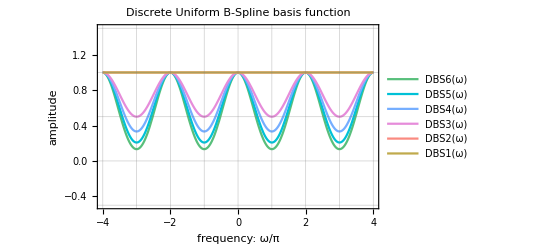

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete Uniform B-Spline basis function (FD).svg

```mathematica
graℱDBS1=Plot[Legended[ℱDBS1[π ω],"DBS1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
graℱDBS2=Plot[Legended[ℱDBS2[π ω],"DBS2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
graℱDBS3=Plot[Legended[ℱDBS3[π ω],"DBS3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
graℱDBS4=Plot[Legended[ℱDBS4[π ω],"DBS4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graℱDBS5=Plot[Legended[ℱDBS5[π ω],"DBS5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
graℱDBS6=Plot[Legended[ℱDBS6[π ω],"DBS6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱDBS=Show[graℱDBS6,graℱDBS5,graℱDBS4,graℱDBS3,graℱDBS2,graℱDBS1,PlotLabel->"Discrete Uniform B-Spline basis function",Frame->True,FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete Uniform B-Spline basis function (FD).svg"}],graℱDBS]
```

## ▼ Discrete High-Enhancement Filter function

## Frequency domain

```mathematica
ℱDHE1[ω_]=1/ℱDBS1[ω]
ℱDHE2[ω_]=1/ℱDBS2[ω]
ℱDHE3[ω_]=1/ℱDBS3[ω]
ℱDHE4[ω_]=1/ℱDBS4[ω]
ℱDHE5[ω_]=1/ℱDBS5[ω]
ℱDHE6[ω_]=1/ℱDBS6[ω]
```

1

1

4/(3+Cos[ω])

3/(2+Cos[ω])

192/(115+76 Cos[ω]+Cos[2 ω])

60/(33+26 Cos[ω]+Cos[2 ω])

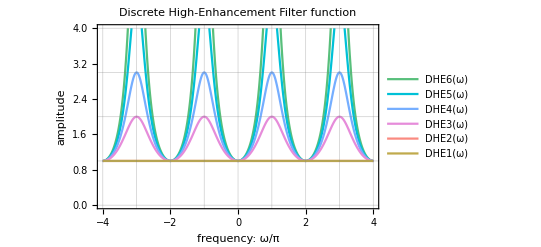

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete High-Enhancement Filter function (FD).svg

```mathematica
graℱDHE1= Plot[Legended[ℱDHE1[π ω],"DHE1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
graℱDHE2= Plot[Legended[ℱDHE2[π ω],"DHE2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
graℱDHE3= Plot[Legended[ℱDHE3[π ω],"DHE3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
graℱDHE4= Plot[Legended[ℱDHE4[π ω],"DHE4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graℱDHE5= Plot[Legended[ℱDHE5[π ω],"DHE5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
graℱDHE6= Plot[Legended[ℱDHE6[π ω],"DHE6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱDHE=Show[graℱDHE6,graℱDHE5,graℱDHE4,graℱDHE3,graℱDHE2,graℱDHE1,PlotLabel->"Discrete High-Enhancement Filter function", Frame->True, FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[0,4,1]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete High-Enhancement Filter function (FD).svg"}],graℱDHE]
```

## Spatial domain

```mathematica
𝒻DHE1[i_]=FourierCosCoefficient[ℱDHE1[ω],ω,i]/2
𝒻DHE2[i_]=FourierCosCoefficient[ℱDHE2[ω],ω,i]/2
𝒻DHE3[i_]=FourierCosCoefficient[ℱDHE3[ω],ω,i]/2
𝒻DHE4[i_]=FourierCosCoefficient[ℱDHE4[ω],ω,i]/2
```

DiscreteDelta[i]

DiscreteDelta[i]

2 HypergeometricPFQRegularized[{1/2,1,1},{1-i,1+i},-1]

3 HypergeometricPFQRegularized[{1/2,1,1},{1-i,1+i},-2]

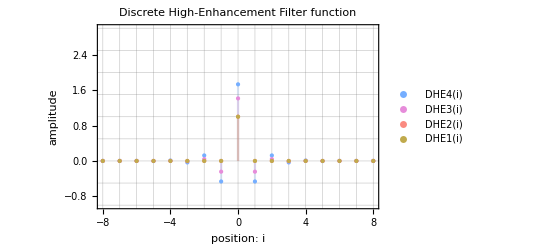

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete High-Enhancement Filter function (SD).svg

```mathematica
gra𝒻DHE1=DiscretePlot[Legended[𝒻DHE1[i],"DHE1(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[192/255,170/255,076/255]}];
gra𝒻DHE2=DiscretePlot[Legended[𝒻DHE2[i],"DHE2(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[250/255,138/255,128/255]}];
gra𝒻DHE3=DiscretePlot[Legended[𝒻DHE3[i],"DHE3(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
gra𝒻DHE4=DiscretePlot[Legended[𝒻DHE4[i],"DHE4(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
gra𝒻DHE=Show[gra𝒻DHE4,gra𝒻DHE3,gra𝒻DHE2,gra𝒻DHE1,PlotLabel->"Discrete High-Enhancement Filter function",Frame->True,FrameLabel->{"position: i","amplitude"},GridLines->{Range[-8,+8,1],Range[-1,+3,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete High-Enhancement Filter function (SD).svg"}],gra𝒻DHE]
```

## ▼ Continuous High-Enhancement Filter function

```mathematica
abs𝒻CHE3[x_]=𝒻DHE3[0]Exp[Log[-𝒻DHE3[1]/𝒻DHE3[0]]Abs[x]]
abs𝒻CHE4[x_]=𝒻DHE4[0]Exp[Log[-𝒻DHE4[1]/𝒻DHE4[0]]Abs[x]]
```

2^(1/2-Abs[x]/2) (-4+3 √2)^Abs[x]

3^(1/2-Abs[x]/2) (-3+2 √3)^Abs[x]

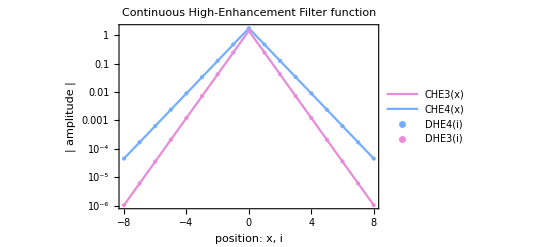

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous High-Enhancement Filter function (AbsSD).svg

```mathematica
rangeN :=8;
graAbs𝒻CHE3=LogPlot[Legended[abs𝒻CHE3[i],"CHE3(x)"],{i,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{RGBColor[230/255,140/255,218/255]}];
graAbs𝒻CHE4=LogPlot[Legended[abs𝒻CHE4[i],"CHE4(x)"],{i,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graAbs𝒻DHE3=ListLogPlot[Legended[Table[{i,Abs[𝒻DHE3[i]]},{i,-rangeN,+rangeN}],"DHE3(i)"],PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
graAbs𝒻DHE4=ListLogPlot[Legended[Table[{i,Abs[𝒻DHE4[i]]},{i,-rangeN,+rangeN}],"DHE4(i)"],PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
graAbs𝒻DHE=Show[graAbs𝒻CHE3,graAbs𝒻CHE4,graAbs𝒻DHE4,graAbs𝒻DHE3,PlotLabel->"Continuous High-Enhancement Filter function", Frame->True, FrameLabel->{"position: x, i","| amplitude |"}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous High-Enhancement Filter function (AbsSD).svg"}],graAbs𝒻DHE]
```

```mathematica
𝒻CHE3[x_]=(-1)^Abs[x] abs𝒻CHE3[x]
𝒻CHE4[x_]=(-1)^Abs[x] abs𝒻CHE4[x]
```

2^(1/2-Abs[x]/2) (4-3 √2)^Abs[x]

3^(1/2-Abs[x]/2) (3-2 √3)^Abs[x]

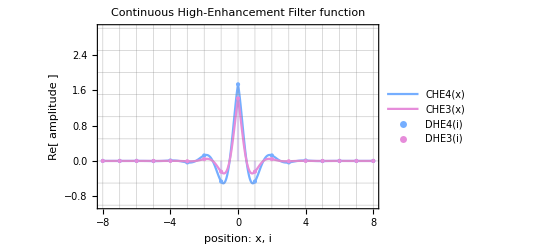

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous High-Enhancement Filter function (SD).svg

```mathematica
gra𝒻CHE3=Plot[Legended[Re[𝒻CHE3[x]],"CHE3(x)"],{x,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{-1,+3}},PlotStyle->{RGBColor[230/255,140/255,218/255]}];
gra𝒻CHE4=Plot[Legended[Re[𝒻CHE4[x]],"CHE4(x)"],{x,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{-1,+3}},PlotStyle->{RGBColor[117/255,174/255,255/255]}];
gra𝒻CHE=Show[gra𝒻CHE4,gra𝒻CHE3,gra𝒻DHE4,gra𝒻DHE3,PlotLabel->"Continuous High-Enhancement Filter function", Frame->True, FrameLabel->{"position: x, i","Re[ amplitude ]"},GridLines->{Range[-8,+8,1],Range[-1,+3,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous High-Enhancement Filter function (SD).svg"}],gra𝒻CHE]
```

## ▼ Approximate Discrete High-Enhancement Filter

## Spatial domain

```mathematica
tapN :=8;
```

```mathematica
tapAHE1=Table[𝒻DHE1[i],{i,0,tapN}]
tapAHE2=Table[𝒻DHE2[i],{i,0,tapN}]
tapAHE3=Table[𝒻DHE3[i],{i,0,tapN}]
tapAHE4=Table[𝒻DHE4[i],{i,0,tapN}]
```

{1,0,0,0,0,0,0,0,0}

{1,0,0,0,0,0,0,0,0}

{√2,4-3 √2,-24+17 √2,140-99 √2,-816+577 √2,4756-3363 √2,-27720+19601 √2,161564-114243 √2,-941664+665857 √2}

{√3,3-2 √3,-12+7 √3,45-26 √3,-168+97 √3,627-362 √3,-2340+1351 √3,8733-5042 √3,-32592+18817 √3}

```mathematica
𝒻AHE1[i_]=If[-tapN≤i≤+tapN,tapAHE1[[1+Abs[i]]],0];
𝒻AHE2[i_]=If[-tapN≤i≤+tapN,tapAHE2[[1+Abs[i]]],0];
𝒻AHE3[i_]=If[-tapN≤i≤+tapN,tapAHE3[[1+Abs[i]]],0];
𝒻AHE4[i_]=If[-tapN≤i≤+tapN,tapAHE4[[1+Abs[i]]],0];
```

## Frequency domain

```mathematica
ℱAHE1[ω_]=FullSimplify[FourierSequenceTransform[𝒻AHE1[i],i,ω]]
ℱAHE2[ω_]=FullSimplify[FourierSequenceTransform[𝒻AHE2[i],i,ω]]
ℱAHE3[ω_]=FullSimplify[FourierSequenceTransform[𝒻AHE3[i],i,ω]]
ℱAHE4[ω_]=FullSimplify[FourierSequenceTransform[𝒻AHE4[i],i,ω]]
```

1

1

√2+(8-6 √2) Cos[ω]+(-48+34 √2) Cos[2 ω]+2 (140-99 √2) Cos[3 ω]+2 (-816+577 √2) Cos[4 ω]+(9512-6726 √2) Cos[5 ω]+2 (-27720+19601 √2) Cos[6 ω]+2 (161564-114243 √2) Cos[7 ω]+2 (-941664+665857 √2) Cos[8 ω]

√3+(6-4 √3) Cos[ω]+2 (-12+7 √3) Cos[2 ω]+(90-52 √3) Cos[3 ω]+2 (-168+97 √3) Cos[4 ω]+2 (627-362 √3) Cos[5 ω]+(-4680+2702 √3) Cos[6 ω]+2 (8733-5042 √3) Cos[7 ω]+2 (-32592+18817 √3) Cos[8 ω]

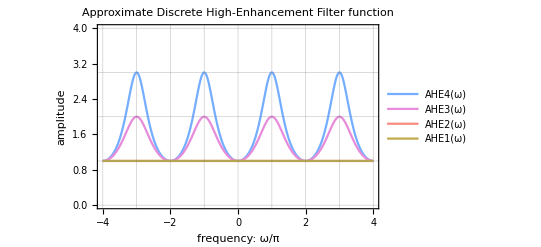

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Approximate Discrete High-Enhancement Filter function (FD).svg

```mathematica
graℱAHE1= Plot[Legended[ℱAHE1[π ω],"AHE1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
graℱAHE2= Plot[Legended[ℱAHE2[π ω],"AHE2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
graℱAHE3= Plot[Legended[ℱAHE3[π ω],"AHE3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
graℱAHE4= Plot[Legended[ℱAHE4[π ω],"AHE4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graℱAHE=Show[graℱAHE4,graℱAHE3,graℱAHE2,graℱAHE1,PlotLabel->"Approximate Discrete High-Enhancement Filter function", Frame->True, FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[0,4,1]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Approximate Discrete High-Enhancement Filter function (FD).svg"}],graℱAHE]
```